# EWS Analysis of Fish Model

## Setup

```mathematica
(* Set Directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transiitons_16/fish_project"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};

(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* Figure parameters *)
{padLeft,padRight,padBottom,padTop}={80,30,40,30};
ldepth=0.9; (* depth of lines where psd measured *)
```

## Simulation data from Matlab (Dakos code)

### Import Data

Data has rows (realisation 1, realisation 2, ... , realisation n)

```mathematica
(* Time series of multiple realisations of exploited population *)
expSeries=Import["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transiitons_16/fish_project/matlab_files/sim_data/Ricker_changeF_sr0.05_se0.1.csv"]//Transpose;
```

```mathematica
(* Time series of multiple realisations of population undergoing increasing growth rate *)
trunSeries=Import["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transiitons_16/fish_project/matlab_files/sim_data/Ricker_changer_sr0.05_se0.1.csv"]//Transpose;
```

```mathematica
expSeries//Dimensions
```

{1000,1000}

### Single Realisation Plots

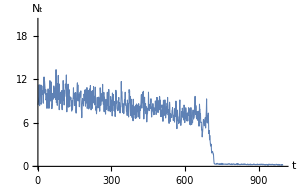

```mathematica
plotSingleExp=ListLinePlot[expSeries[[1]],
ImageSize->300,
PlotStyle->Thickness[0.0025],
PlotRange->{0,20},
LabelStyle->14,
AxesLabel->{"t","N_t"}]
```

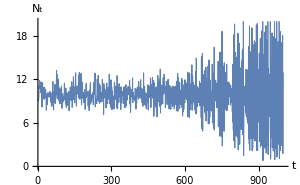

```mathematica
plotSingleTrun=ListLinePlot[trunSeries[[1]],
ImageSize->300,
PlotStyle->Thickness[0.0025],
PlotRange->{0,20},
LabelStyle->14,
AxesLabel->{"t","N_t"}]
```

## Simulation Indicators - Exploitation

### Key values / parameters

```mathematica
(* no. realisations *)
iter=10;

(* control parameter range *)
fl=0;
fh=3;
tmax=1000;
(* saddle node bifurcation values *)
fcrit1=2.364; 
fcrit2=1.491;
(* transition time *)
tcritExp=Floor[(fcrit1-fl)*tmax /(fh-fl)];

(* details on EWS *)
detrendOp=0;
bandWidth=0.1; (* for Gaussian filter (fraction of timeseries) *)
rollWindow=0.2; (* rolling window for stat metrics (fraction of timeseries *)
tauVals={1,2}; (* lag times for autocorrelation *)

(* plot parameters *)
aHeadSize=0.03;
```

### Detrending Process (Gaussian Filter)

```mathematica
(* Detrend data up to transition *) 
tVals=Range[1,tmax];
dataFitExp=If[detrendOp==1,
Table[
GaussianFilter[expSeries[[i,1;;tcritExp]],tcritExp*bandWidth],
{i,1,iter}],
ConstantArray[0,{iter,tcritExp}]
];
```

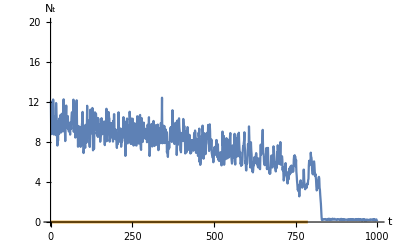

```mathematica
(* plot of single realisation *)
plotNum=2;
ListLinePlot[{expSeries[[plotNum]],dataFitExp[[plotNum]]},
ImageSize->400,
LabelStyle->14,
AxesLabel->{"t","N_t"},
PlotRange->{{0,tmax},{0,20}},
PlotStyle->{Default,Thickness[0.005]},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

```mathematica
(* compute residuals of series *)
residualsExp=expSeries[[1;;iter,1;;tcritExp]]-dataFitExp;
```

### Variance

```mathematica
(* number of component in the rolling window *)
windowComps=Floor[rollWindow*tcritExp];
varSeries=Table[MovingMap[Variance,residualsExp[[i]],windowComps],{i,1,iter}];
meanSeries=Table[MovingMap[Mean,expSeries[[i,1;;tcritExp]],windowComps],{i,1,iter}];
cvSeries = varSeries/meanSeries;
```

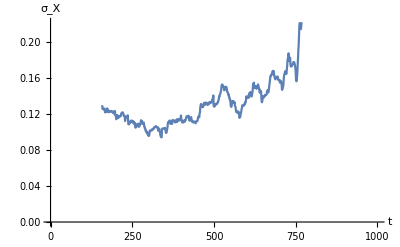

```mathematica
(* single plot *)
ListPlot[{tVals[[windowComps+1;;tcritExp]],cvSeries[[2]]}ᵀ, (* to account for the rolling window *)
Joined->True,
AxesLabel->{"t","σ_X"},
LabelStyle->14,
ImageSize->400,
PlotRange->{{0,tmax},Automatic}]
```

```mathematica
(* Over all simulations *)
meanCVseries=Mean[cvSeries];
devCVseries=StandardDeviation[cvSeries];
```

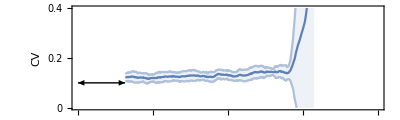

```mathematica
cvPlotExp=ListPlot[{{tVals[[windowComps+1;;tcritExp]],meanCVseries}ᵀ,
{tVals[[windowComps+1;;tcritExp]],meanCVseries+devCVseries}ᵀ,
{tVals[[windowComps+1;;tcritExp]],meanCVseries-devCVseries}ᵀ},
Joined->True,
PlotStyle->{TMBcolours⟦1⟧,Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5]},
Filling->{{2->{1}},{3->{1}}},
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},{0,0.4}},
FrameLabel->{{"CV",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5},Automatic},{Automatic,Automatic}},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{{0,0.1},{windowComps,0.1}}]}]
```

### Autocorrelation of Residuals at various lags

```mathematica
(* form [a1;a2;,,,;an] *)
acSeries=Table[MovingMap[CorrelationFunction[#,tauVals[[j]]]&,residualsExp[[i]],windowComps],{i,1,iter},{j,1,Length[tauVals]}]; 
acSeries//Dimensions
(* sim number, lag number, time value *)
```

{10,2,630}

```mathematica
(* line legend *)
legend=LineLegend[TMBcolours[[1;;2]],{"τ=1","τ=2"}]
```

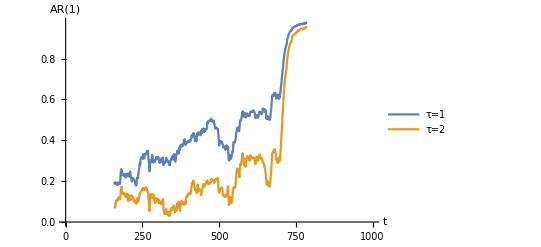

```mathematica
(* plot *)
acPlot=ListPlot[Table[{tVals[[windowComps+1;;tcritExp]],acSeries[[1,j]]}ᵀ,{j,1,Length[tauVals]}],
Joined->True,
AxesLabel->{"t","AR(1)"},
LabelStyle->14,
ImageSize->400,
PlotRange->{{0,tmax},All},
PlotLegends->Placed[legend,{0.2,0.7}]]
```

```mathematica
(* a plot averaged over simulations *)
meanACseries=Table[Mean[acSeries[[;;,j]]],{j,1,Length[tauVals]}];
devACseries=If[iter>1,Table[StandardDeviation[acSeries[[;;,j]]],{j,1,Length[tauVals]}],
ConstantArray[0,Length[meanACseries]]];
meanACseries//Dimensions
```

{2,630}

```mathematica
(* ac plot as a function of lag *)
Clear[acPlot];
acPlot[j_]:=ListPlot[{
{tVals[[windowComps+1;;tcritExp]],meanACseries[[j]]}ᵀ,
{tVals[[windowComps+1;;tcritExp]],meanACseries[[j]]+devACseries[[j]]}ᵀ,
{tVals[[windowComps+1;;tcritExp]],meanACseries[[j]]-devACseries[[j]]}ᵀ},
Joined->True,
PlotStyle->{TMBcolours[[j]],Lighter[TMBcolours[[j]],0.5],Lighter[TMBcolours[[j]],0.5]},
Filling->{{2->{1}},{3->{1}}},
LabelStyle->14,
Frame->True,
FrameLabel->{{"AC",""},{"",""}},
PlotRange->{{0,tmax},All},
PlotRangeClipping->False,
PlotLegends->If[j==1,Placed[legend,{0.12,0.7}],None]];
```

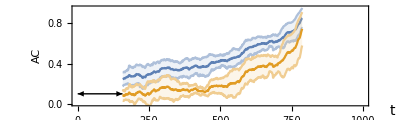

```mathematica
acPlotLagsExp=Show[Table[acPlot[i],{i,1,Length[tauVals]}],
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
Ticks->{Default,{0,0.4,0.8}},
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{{0,0.1},{windowComps,0.1}}],
Text[Style["t",14],Scaled[{1.08,-0.05}]]}]
```

### Power Spectral Density

```mathematica
(* psd parameters *)
Clear[ω]
psdTimeVals={300,450,600};
cutoff=15;
(* range of frequencies in power spectrum *)
ωVals=Range[-Pi,Pi,0.01];
```

```mathematica
residualsExp//Dimensions
```

{10,787}

```mathematica
(* function for psd in terms of ω for realisation i and time value j *)
Clear[psd];
psd[ω_,i_,j_]:=PowerSpectralDensity[residualsExp[[i,psdTimeVals[[j]]-windowComps;;psdTimeVals[[j]]]],ω,cutoff,FourierParameters->{-1,1}];
```

```mathematica
(* convert this to data (not functional) form *)
psdSeriesExp=Table[psd[ω,i,j],{i,1,iter},{j,1,Length[psdTimeVals]},{ω,ωVals}];
```

```mathematica
psdSeriesExp//Dimensions
```

{10,3,629}

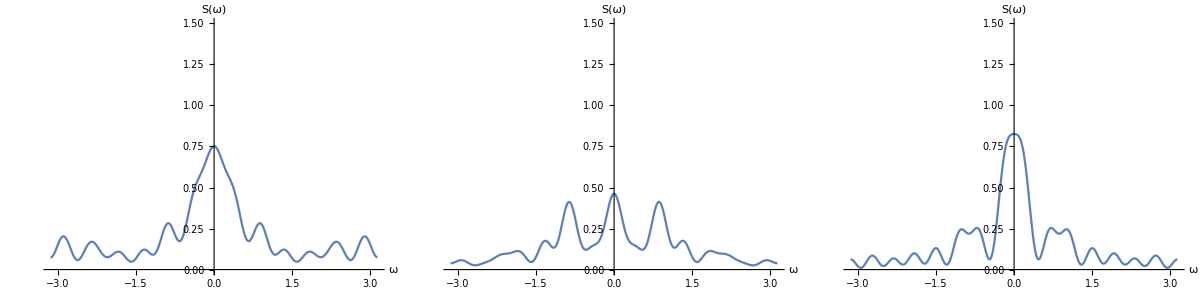

```mathematica
(* single-realisation plot *)
Grid[{Table[
ListLinePlot[Transpose[{ωVals,psdSeriesExp[[5,j]]}],
ImageSize->200,
PlotRange->{0,1.5},
AspectRatio->1.2,
LabelStyle->14,
AxesLabel->{"ω","S(ω)"}],
{j,1,Length[psdTimeVals]}]}]
```

```mathematica
(* take averages over realisations *)
meanPsd=Mean[psdSeriesExp];
devPsd=StandardDeviation[psdSeriesExp];
```

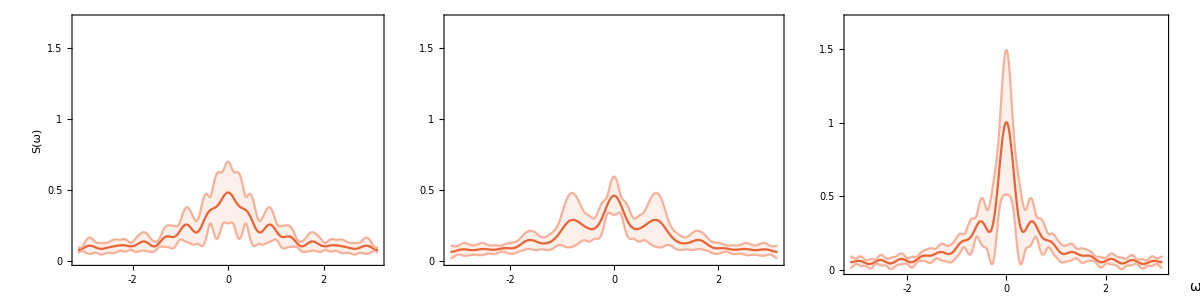

```mathematica
(* Plot with error bars of 1 s.d. *)
plotPsdExp=Grid[{Table[
ListLinePlot[{Transpose[{ωVals,meanPsd[[j]]}],
Transpose[{ωVals,meanPsd[[j]]+devPsd[[j]]}],
Transpose[{ωVals,meanPsd[[j]]-devPsd[[j]]}]},
Joined->True,
ImageSize->160,
AspectRatio->1.2,
PlotRange->{0,1.7},
PlotStyle->{TMBcolours⟦4⟧,Lighter[TMBcolours⟦4⟧,0.5],Lighter[TMBcolours⟦4⟧,0.5]},
Filling->{{2->{1}},{3->{1}}},
AspectRatio->1.2,
LabelStyle->14,
Frame->True,
FrameLabel->If[j==1,{{"S(ω)",""},{"",""}}],
Epilog->If[j==3,Text[Style["ω",14],Scaled[{1.08,-0.05}]],Text[Style["ω",14,White],Scaled[{1.02,-0.1}]]],
PlotRangeClipping->False,
ImagePadding->{{45,20},{40,40}},
FrameTicksStyle->If[j≥2,{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}},{{Automatic,Automatic},{Automatic,Automatic}}],
FrameTicks->{{{0,0.5,1,1.5},Automatic},{{-2,0,2},Automatic}}
],
{j,1,Length[psdTimeVals]}]},Spacings->{-3,0}]
```

## Bifurcation Diagram (exploited pop)

Deterministic model is
N_(t+1)=N_t e^(r(1-N_t/K))-F N_t^2/(N_t^2+h^2)

### Specifications

```mathematica
Import["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transiitons_16/fish_project/bifurcation/fish_exp.dat"];
```

```mathematica
(* Import data *)
rawdata=Import["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transiitons_16/fish_project/bifurcation/fish_exp.dat"];



(* plotting spec *)
lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
imgs=400; (* image size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{0,3},{0,20}}; (* plot range *)
(*frLabel={"F","N"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
{padLeft,padRight,padBottom,padTop}={80,30,40,30};
```

### Line Plot

```mathematica
Range[0,3,3/1000]//Dimensions
```

{1001}

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdata[[;;,{1,2,4,5}]],rawdata[[;;,{1,3,4,5}]]]//DeleteDuplicates;
(* Data using t instead of F *)
fbifVals=fulldata[[;;,1]];
tbifVals=(fbifVals-fl)*tmax /(fh-fl);
fulldataT=ReplacePart[Transpose[fulldata],1->tbifVals]//Transpose;
```

```mathematica
(* Stability type of point i *)
stabType=fulldataT[[;;,3]];
```

```mathematica
numPoints=Length[fulldataT];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldataT[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldataT⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
(* Adjust certain branches *)
(*nodeSections[[3]]=Cases[nodeSections[[3]],{x_,_,_,_}/; x>0] ; 
nodeSections=Append[nodeSections,Cases[nodeSections[[6]],{_,x_,_,_}/;x>0]];
nodeSections[[6]]=Cases[nodeSections[[6]],{_,x_,_,_}/;x<0]; *)(* had to seperate out branches for plotting purposes *)
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
(* Stabilty of sections *)
stab=Table[nodeSections[[i,1,3]],{i,1,numBranches}]
```

{2,1,2,1}

```mathematica
(* Take relevant branches of node sections *)
delList={};
branchesNums=Complement[Range[1,numBranches],delList]
```

{1,2,3,4}

```mathematica
(* Color vector *)
colorScheme=eqColors[[stab[[branchesNums]]]];
```

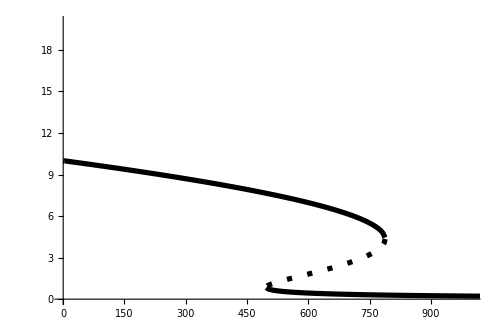

```mathematica
(* Make plot *)
bifPlotExp=ListCurvePathPlot[Join[nodeSections[[branchesNums]]],
PlotStyle->Transpose[{colorScheme,ConstantArray[Thickness[lt],Length[colorScheme]]}],
LabelStyle->font,
InterpolationOrder->None,
PlotRange->{{0,1000},{0,20}},
Axes->{True,True},
ImageSize->{500,300},
AspectRatio->2/3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}
]
```

### Incorporate bif diagram with Simulation

```mathematica
arHeight=ldepth+(1-ldepth)/2;
arLength=windowComps;
lineStyle={TMBcolours[[4]],Opacity[1]};
```

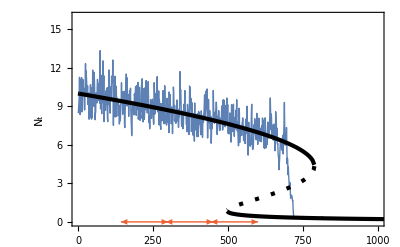

```mathematica
(* Incorporate with simulation *)
figBifTrajExp=Show[{plotSingleExp,bifPlotExp},
PlotRange->{{0,tmax},{0,16}},
LabelStyle->14,
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"N_t",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Directive[lineStyle],Arrowheads[{-aHeadSize,aHeadSize}],
Table[Line[{Scaled[{0,ldepth},{psdTimeVals[[j]],0}],Scaled[{0,1},{psdTimeVals[[j]],0}]}],{j,1,3}],
Table[Arrow[{Scaled[{0,arHeight},{psdTimeVals[[j]]-windowComps,0}],Scaled[{0,arHeight},{psdTimeVals[[j]],0}]}],{j,1,3}]}]
```

## Simulation Indicators - Truncation

### Key values / parameters

```mathematica
(* no. realisations *)
iter=10;

(* control parameter range *)
rl=0.5;
rh=2.6;
tmax=1000;
(* PD bifurcation values *)
rcrit1=2; 
rcrit2=2.526;
(* transition times *)
tcritTrun=Floor[(rcrit1-rl)*tmax /(rh-rl)];

(* details on EWS *)
detrendOp=0;
bandWidth=0.1; (* for Gaussian filter (fraction of timeseries) *)
rollWindow=0.2; (* rolling window for stat metrics (fraction of timeseries *)
tauVals={1,2}; (* lag times for autocorrelation *)

(* plot parameters *)
aHeadSize=0.03;
```

### Detrending Process (Gaussian Filter)

```mathematica
(* Detrend data up to transition *) 
tVals=Range[1,tmax];
dataFitTrun=If[detrendOp==1,
Table[
GaussianFilter[trunSeries[[i,1;;tcritTrun]],tcritTrun*bandWidth],
{i,1,iter}],
ConstantArray[0,{iter,tcritTrun}]
];
```

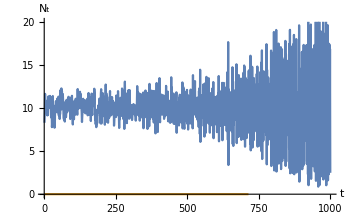

```mathematica
(* plot of single realisation *)
plotNum=2;
ListLinePlot[{trunSeries[[plotNum]],dataFitTrun[[plotNum]]},
ImageSize->350,
LabelStyle->14,
AxesLabel->{"t","N_t"},
PlotRange->{{0,tmax},{0,20}},
PlotStyle->{Default,Default},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

```mathematica
dataFitTrun//Dimensions
```

{10,714}

```mathematica
trunSeries[[;;,1;;tcritTrun]]//Dimensions
```

{1000,714}

```mathematica
(* compute residuals of series *)
residualsTrun=trunSeries[[1;;iter,1;;tcritTrun]]-dataFitTrun;
```

### Variance

```mathematica
(* number of component in the rolling window *)
windowComps=Floor[rollWindow*tcritTrun];
varSeries=Table[MovingMap[Variance,residualsTrun[[i]],windowComps],{i,1,iter}];
meanSeries=Table[MovingMap[Mean,trunSeries[[i,1;;tcritTrun]],windowComps],{i,1,iter}];
cvSeries = varSeries/meanSeries;
```

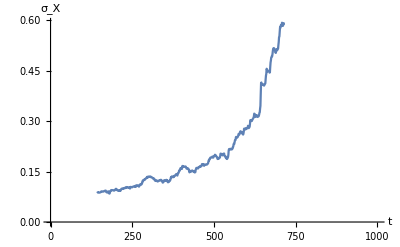

```mathematica
(* single plot *)
ListPlot[{tVals[[windowComps+1;;tcritTrun]],cvSeries[[2]]}ᵀ, (* to account for the rolling window *)
Joined->True,
AxesLabel->{"t","σ_X"},
LabelStyle->14,
ImageSize->400,
PlotRange->{{0,tmax},Automatic}]
```

```mathematica
(* Over all simulations *)
meanCVseries=Mean[cvSeries];
devCVseries=StandardDeviation[cvSeries];
```

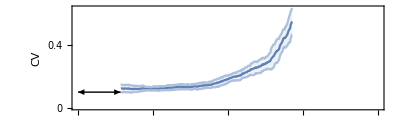

```mathematica
cvPlotTrun=ListPlot[{{tVals[[windowComps+1;;tcritTrun]],meanCVseries}ᵀ,
{tVals[[windowComps+1;;tcritTrun]],meanCVseries+devCVseries}ᵀ,
{tVals[[windowComps+1;;tcritTrun]],meanCVseries-devCVseries}ᵀ},
Joined->True,
PlotStyle->{TMBcolours⟦1⟧,Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5]},
Filling->{{2->{1}},{3->{1}}},
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},All},
FrameLabel->{{"CV",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
FrameTicks->{{{{0,0},0.2,0.4,0.6,0.8},Automatic},{Automatic,Automatic}},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{{0,0.1},{windowComps,0.1}}]}]
```

### Autocorrelation of Residuals at various lags

```mathematica
(* form [a1;a2;,,,;an] *)
acSeries=Table[MovingMap[CorrelationFunction[#,tauVals[[j]]]&,residualsTrun[[i]],windowComps],{i,1,iter},{j,1,Length[tauVals]}]; 
acSeries//Dimensions
(* sim number, lag number, time value *)
```

{10,2,572}

```mathematica
(* line legend *)
legend=LineLegend[TMBcolours[[1;;2]],{"τ=1","τ=2"}]
```

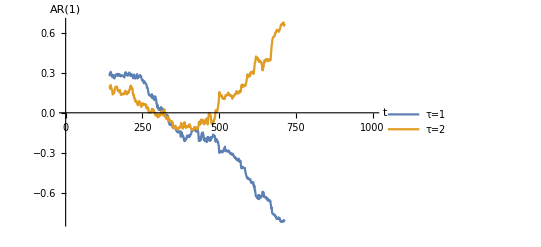

```mathematica
(* plot *)
acPlot=ListPlot[Table[{tVals[[windowComps+1;;tcritTrun]],acSeries[[1,j]]}ᵀ,{j,1,Length[tauVals]}],
Joined->True,
AxesLabel->{"t","AR(1)"},
LabelStyle->14,
ImageSize->400,
PlotRange->{{0,tmax},All},
PlotLegends->Placed[legend,{0.2,0.7}]]
```

```mathematica
(* a plot averaged over simulations *)
meanACseries=Table[Mean[acSeries[[;;,j]]],{j,1,Length[tauVals]}];
devACseries=If[iter>1,Table[StandardDeviation[acSeries[[;;,j]]],{j,1,Length[tauVals]}],
ConstantArray[0,Length[meanACseries]]];
meanACseries//Dimensions
```

{2,572}

```mathematica
(* ac plot as a function of lag *)
Clear[acPlot];
acPlot[j_]:=ListPlot[{
{tVals[[windowComps+1;;tcritTrun]],meanACseries[[j]]}ᵀ,
{tVals[[windowComps+1;;tcritTrun]],meanACseries[[j]]+devACseries[[j]]}ᵀ,
{tVals[[windowComps+1;;tcritTrun]],meanACseries[[j]]-devACseries[[j]]}ᵀ},
Joined->True,
PlotStyle->{TMBcolours[[j]],Lighter[TMBcolours[[j]],0.5],Lighter[TMBcolours[[j]],0.5]},
Filling->{{2->{1}},{3->{1}}},
LabelStyle->14,
Frame->True,
FrameLabel->{{"AC",""},{"",""}},
PlotRange->{{0,tmax},All},
PlotRangeClipping->False,
PlotLegends->If[j==1,Placed[legend,{0.12,0.24}],None]];
```

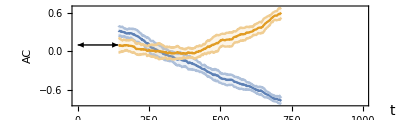

```mathematica
acPlotLagsTrun=Show[Table[acPlot[i],{i,1,Length[tauVals]}],
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
PlotRange->{{0,tmax},All},
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{{0,0.1},{windowComps,0.1}}],
Text[Style["t",14],Scaled[{1.08,-0.05}]]}]
```

### Power Spectral Density

```mathematica
(* psd parameters *)
Clear[ω]
psdTimeVals={300,450,600};
cutoff=15;
(* range of frequencies in power spectrum *)
ωVals=Range[-2Pi,2Pi,0.01];
```

```mathematica
(* function for psd in terms of ω for realisation i and time value j *)
Clear[psd];
psd[ω_,i_,j_]:=PowerSpectralDensity[residualsTrun[[i,psdTimeVals[[j]]-windowComps;;psdTimeVals[[j]]]],ω,cutoff,FourierParameters->{-1,1}];
```

```mathematica
(* convert this to data (not functional) form *)
psdSeriesTrun=Table[psd[ω,i,j],{i,1,iter},{j,1,Length[psdTimeVals]},{ω,ωVals}];
```

```mathematica
psdSeriesTrun//Dimensions
```

{10,3,1257}

```mathematica
(*Epilog->If[j≥1,Text[Style["ω",14],Scaled[{1.03,-0.1}]],None]*)
```

```mathematica
(*ImagePadding->{{padLeft,padRight},{padBottom,padTop}}*)
```

```mathematica
(* If[j==3,Text[Style["ω",14],Scaled[{1.09,-0.05}]],None],*)
```

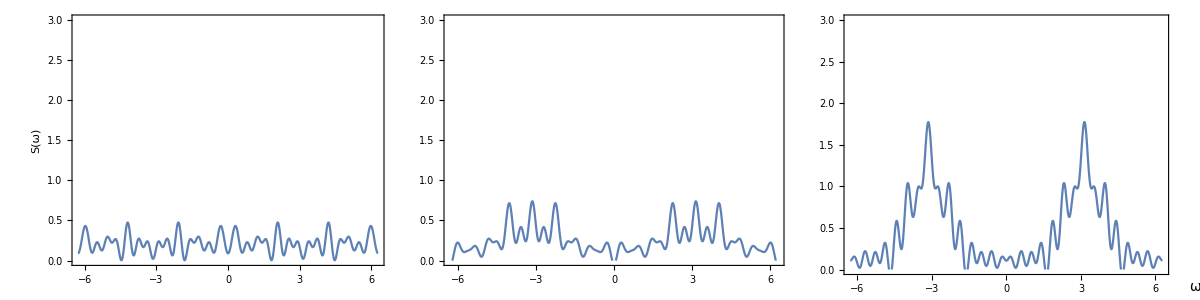

```mathematica
(* single-realisation plot *)
psdPlot=Grid[{Table[
ListLinePlot[Transpose[{ωVals,psdSeriesTrun[[plotNum,j]]}],
ImageSize->200,
AspectRatio->1.2,
PlotRange->{0,3},
AspectRatio->1.2,
LabelStyle->14,
Frame->True,
FrameLabel->If[j==1,{{"S(ω)",""},{"",""}}],
Epilog->If[j==3,Text[Style["ω",14],Scaled[{1.08,-0.05}]],Text[Style["ω",14,White],Scaled[{1.02,-0.1}]]],
PlotRangeClipping->False,
ImagePadding->{{45,20},{20,20}},
FrameTicksStyle->If[j≥2,{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}},{{Automatic,Automatic},{Automatic,Automatic}}]
],
{j,1,Length[psdTimeVals]}]},Spacings->{-3,0}]
```

```mathematica
(* take averages over realisations *)
meanPsd=Mean[psdSeriesTrun];
devPsd=StandardDeviation[psdSeriesTrun];
```

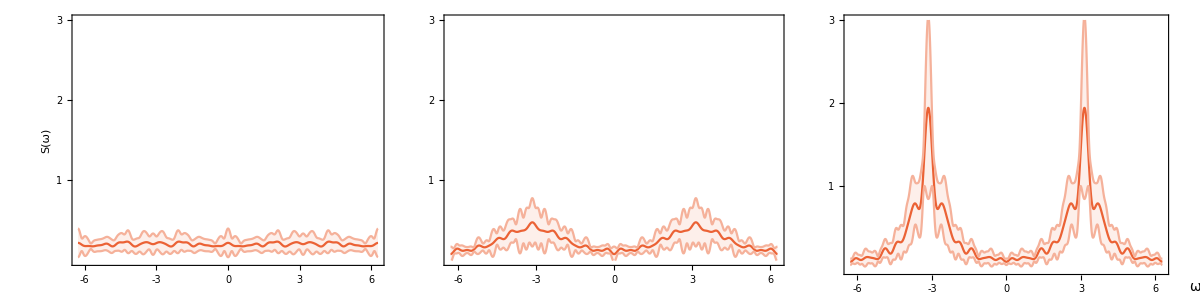

```mathematica
(* single-realisation plot *)
plotPsdTrun=Grid[{Table[
ListLinePlot[{Transpose[{ωVals,meanPsd[[j]]}],
Transpose[{ωVals,meanPsd[[j]]+devPsd[[j]]}],
Transpose[{ωVals,meanPsd[[j]]-devPsd[[j]]}]},
Joined->True,
ImageSize->160,
AspectRatio->1.2,
PlotRange->{0,3},
PlotStyle->{TMBcolours⟦4⟧,Lighter[TMBcolours⟦4⟧,0.5],Lighter[TMBcolours⟦4⟧,0.5]},
Filling->{{2->{1}},{3->{1}}},
AspectRatio->1.2,
LabelStyle->14,
Frame->True,
FrameLabel->If[j==1,{{"S(ω)",""},{"",""}}],
Epilog->If[j==3,Text[Style["ω",14],Scaled[{1.08,-0.05}]],Text[Style["ω",14,White],Scaled[{1.02,-0.1}]]],
PlotRangeClipping->False,
ImagePadding->{{45,20},{40,40}},
FrameTicksStyle->If[j≥2,{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}},{{Automatic,Automatic},{Automatic,Automatic}}],
FrameTicks->{{{1,2,3},Automatic},{{-6,-3,0,3,6},Automatic}}
],
{j,1,Length[psdTimeVals]}]},Spacings->{-3,0}]
```

## Bifurcation Diagram (truncated growth)

Deterministic model is
N_(t+1)=N_t e^(r(1-N_t/K))-F N_t^2/(N_t^2+h^2)

### Specifications

```mathematica
(* Import data *)
rawdata=Import["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transiitons_16/fish_project/bifurcation/fish_trun.dat"];

(* bifurcation parameter range *)
rl=0.1;
rh=2.6;
(* PD bifurcation values *)
rcrit1=2; 
rcrit2=2.526;
(* time of transition *)
tcritTrun=(rcrit1-rl)*tmax /(rh-rl);

(* plotting spec *)
lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
imgs=400; (* image size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{0,3},{0,20}}; (* plot range *)
(*frLabel={"F","N"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{1lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
{padLeft,padRight,padBottom,padTop}={80,30,40,30};
```

### Line Plot

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdata[[;;,{1,2,4,5}]],rawdata[[;;,{1,3,4,5}]]]//DeleteDuplicates;
(* Data using t instead of F *)
rbifVals=fulldata[[;;,1]];
tbifVals=(rbifVals-rl)*tmax /(rh-rl);
fulldataT=ReplacePart[Transpose[fulldata],1->tbifVals]//Transpose;
```

```mathematica
(* Stability type of point i *)
stabType=fulldataT[[;;,3]];
```

```mathematica
numPoints=Length[fulldataT];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldataT[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldataT⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
(* Adjust certain branches *)
nodeSections[[8]]=Cases[nodeSections[[8]],{x_,_,_,_}/; x<999] ; 
nodeSections[[10]]=Cases[nodeSections[[10]],{x_,_,_,_}/; x<999];
(* had to seperate out branches for plotting purposes *)
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
(* Stabilty of sections *)
stab=Table[nodeSections[[i,1,3]],{i,1,numBranches}]
```

{2,1,2,1,2,1,2,1,2,1}

```mathematica
(* Take relevant branches of node sections *)
delList={5};
branchesNums=Complement[Range[1,numBranches],delList]
```

{1,2,3,4,6,7,8,9,10}

```mathematica
(* Color vector *)
colorScheme=eqColors[[stab[[branchesNums]]]];
```

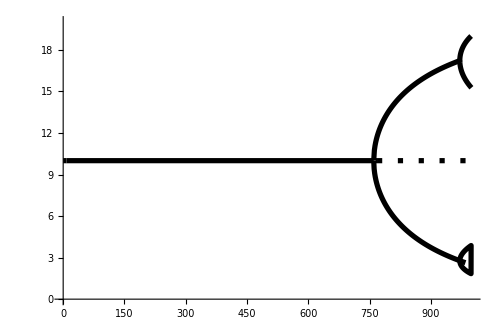

```mathematica
(* Make plot *)
bifPlotTrun=ListCurvePathPlot[Join[nodeSections[[branchesNums]]],
PlotStyle->Transpose[{colorScheme,ConstantArray[Thickness[lt],Length[colorScheme]]}],
LabelStyle->font,
InterpolationOrder->None,
PlotRange->{{0,1000},{0,20}},
Axes->{True,True},
ImageSize->{500,300},
AspectRatio->2/3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}
]
```

### Incorporate bif diagram with Simulation

```mathematica
lineStyle={TMBcolours[[4]],Opacity[1]};
arHeight=ldepth+(1-ldepth)/2;
arLength=windowComps;
```

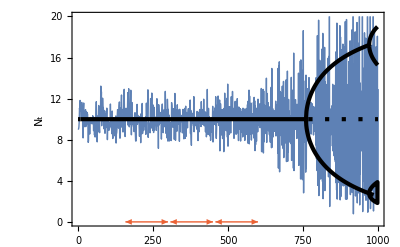

```mathematica
(* Incorporate with simulation *)
figBifTrajTrun=Show[{plotSingleTrun,bifPlotTrun},
PlotRange->{{0,tmax},{0,20}},
LabelStyle->14,
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"N_t",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Directive[lineStyle],Arrowheads[{-aHeadSize,aHeadSize}],
Table[Line[{Scaled[{0,ldepth},{psdTimeVals[[j]],0}],Scaled[{0,1},{psdTimeVals[[j]],0}]}],{j,1,3}],
Table[Arrow[{Scaled[{0,arHeight},{psdTimeVals[[j]]-windowComps,0}],Scaled[{0,arHeight},{psdTimeVals[[j]],0}]}],{j,1,3}]}
]
```

```mathematica
Epilog->If[j==3,Text[Style["ω",14],Scaled[{1.08,-0.05}]],Text[Style["ω",14,White],Scaled[{1.02,-0.1}]]]
```

Epilog→If[j==3,Text[ω,Scaled[{1.08,-0.05}]],Text[Style[ω,14,White],Scaled[{1.02,-0.1}]]]

```mathematica
Scaled
```

Scaled

```mathematica
windowComps
```

142

## Figure Construction

```mathematica
figFishEws=Grid[{{figBifTrajExp,figBifTrajTrun},{cvPlotExp,cvPlotTrun},{acPlotLagsExp,acPlotLagsTrun},{plotPsdExp,plotPsdTrun}},Spacings->{0,-3}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Export["figures/fishEws.png",figFishEws];
```